```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Das folgende Programm gilt für homogene Differentialgleichungssysteme in der Form:

ⅆ/ⅆt 𝓎(t)=𝒜·𝓎(t)

Die Lösung eines allgemeinen Differentialgleichungssystems erhält man wie folgt:

𝓎(t)=ⅇ^(t·𝒜)·(𝓋_0+∫_0^t ⅇ^(-τ·𝒜)·𝓈(τ)ⅆτ)=ⅇ^(t·𝒜)·𝓋_0+∫_0^t ⅇ^((t-τ)·𝒜)·𝓈(τ)ⅆτ=Re[ⅇ^(t·𝒜)]·𝓋_0+∫_0^t Re[ⅇ^((t-τ)·𝒜)]·𝓈(τ)ⅆτ

Durch Diagonalisierung (Auflistung der Eigenvektoren in der Matrix 𝒫 und den Eigenwerten λ auf der Hauptdiagonalen der Diagonalmatrix 𝒟) des Matrixexponentials folgt:

𝓎(t)=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1]·𝓋_0+∫_0^t Re[𝒫·𝒟[ⅇ^(λ·(t-τ))]·𝒫^-1]·𝓈[τ]ⅆτ

Für den homogenen Fall folgt:

𝓎(t)=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1]·𝓋_0=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒫^-1·𝓋_0]=Re[𝒫·𝒟[ⅇ^(λ·t)]·𝒸]=Re[∑_(i=1)^n c_i 𝓅_i ⅇ^(λ_i t)]

Hinweis zum Programm: Realteilbildung von 𝓎(t) optional bereits in der allgemeinen Lösung möglich (ComplexExpand[Re[…]] um die Summe)

## Eingabe (𝒜)

```mathematica
ClearAll["Global`*"]
𝒜=({{0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}, {-6, 0, -5, 0}})//N;
```

## Eingabe (𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃)

Die Nebenbedingungen des Differentialgleichungssystems werden wie folgt defniniert:

```mathematica
𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃=({{Funktion, Zeit, Wert}});
```

```mathematica
𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃=({{1, 0, 0}, {1, 1, 1}, {2, 0, 0}, {2, 1, 0}})//N;
```

```mathematica
(*Ausgabe*)
Print[StringForm["Nebenbedingungen:\n``\n→ Es handelt sich um ein `` Differentialgleichungssystem.",
TableForm[Table[
{Subscript[y, Rationalize[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]},
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}],TableHeadings->{None,{"Funktion","Zeit","Wert"}}],
Which[
Length[𝒜]==Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"bestimmtes",
Length[𝒜]<Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"überbestimmtes",
Length[𝒜]>Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃],"unterbestimmtes"]]]
```

Nebenbedingungen:
Funktion | Zeit | Wert
y_1 | 0. | 0.
y_1 | 1. | 1.
y_2 | 0. | 0.
y_2 | 1. | 0.
→ Es handelt sich um ein bestimmtes Differentialgleichungssystem.

## Programm (allgemein)

```mathematica
(*Programm*)
λ=Chop[Eigenvalues[𝒜]];
𝒫=Chop[Transpose[Eigenvectors[𝒜]]];
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t_]=Sum[Subscript[c, i] 𝒫[[All,i]]Exp[λ[[i]]t],{i,Length[𝒜]}];

(*Ausgabe*)
Print[StringForm["λ = ``\n𝒫 = ``\n𝓎_allgemein(t) = ``",
λ//MatrixForm,
𝒫//MatrixForm,
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]//MatrixForm]]
```

λ = (0.+1.73205 ⅈ
0.-1.73205 ⅈ
0.+1.41421 ⅈ
0.-1.41421 ⅈ)
𝒫 = (0.+0.158114 ⅈ | 0.-0.158114 ⅈ | 0.-0.258199 ⅈ | 0.+0.258199 ⅈ
-0.273861 | -0.273861 | 0.365148 | 0.365148
0.-0.474342 ⅈ | 0.+0.474342 ⅈ | 0.+0.516398 ⅈ | 0.-0.516398 ⅈ
0.821584 | 0.821584 | -0.730297 | -0.730297)
𝓎_allgemein(t) = …

## Programm (bestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[1]]}];
𝒸=Flatten[LinearSolve[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[c, i]->𝒸[[i]],{i,Length[𝒸]}]]]]]/.𝓇ℯℊℯℓ𝓃;

(*Ausgabe*)
Print[StringForm["𝒸 = ``\n𝓎(t) = ``\n``",
𝒸//MatrixForm,
𝓎[t]//MatrixForm,
If[AllTrue[Table[Round[𝓎[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]],N[10^-9]]==Round[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],N[10^-9]],{i,Length[𝒸]}],TrueQ],
Style["→ Probe erfolgreich ☺",Darker[Green]],Style["→ Fehler aufgetreten ☹",Darker[Red]]]]]
```

𝒸 = (-9.51982+16.6909 ⅈ
-9.51982-16.6909 ⅈ
-7.13987+10.221 ⅈ
-7.13987-10.221 ⅈ)
𝓎(t) = (-5.27812 Cos[1.73205 t]+6.43837 Cos[0.609749+1.41421 t]+3.01043 Sin[1.73205 t]
5.21422 Cos[1.73205 t]+9.10523 Cos[2.18055+1.41421 t]+9.14198 Sin[1.73205 t]
12.8767 Cos[2.53184-1.41421 t]+15.8344 Cos[1.73205 t]-9.03129 Sin[1.73205 t]
18.2105 Cos[0.961047-1.41421 t]-15.6427 Cos[1.73205 t]-27.4259 Sin[1.73205 t])
→ Probe erfolgreich ☺

## Programm (überbestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[1]]}];
𝒸=Flatten[LeastSquares[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[c, i]->𝒸[[i]],{i,Length[𝒸]}]]]]]/.𝓇ℯℊℯℓ𝓃;

(*Ausgabe*)
Print[StringForm["𝒸 = ``\n𝓎(t) = ``",
𝒸//MatrixForm,
𝓎[t]//MatrixForm]]
```

𝒸 = (-9.51982+16.6909 ⅈ
-9.51982-16.6909 ⅈ
-7.13987+10.221 ⅈ
-7.13987-10.221 ⅈ)
𝓎(t) = (-5.27812 Cos[1.73205 t]+6.43837 Cos[0.609749+1.41421 t]+3.01043 Sin[1.73205 t]
5.21422 Cos[1.73205 t]+9.10523 Cos[2.18055+1.41421 t]+9.14198 Sin[1.73205 t]
12.8767 Cos[2.53184-1.41421 t]+15.8344 Cos[1.73205 t]-9.03129 Sin[1.73205 t]
18.2105 Cos[0.961047-1.41421 t]-15.6427 Cos[1.73205 t]-27.4259 Sin[1.73205 t])

## Programm (unterbestimmt)

```mathematica
(*Programm*)
ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Table[
𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]][[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,1]]]]==𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[2]];
𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃=-Transpose[{Normal[CoefficientArrays[ℊℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃,Table[Subscript[c, i],{i,Length[𝒜]}]]][[1]]}];
{𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃n}=Dimensions[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃1=𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃[[All,1;;𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m]];
𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃2=𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃[[All,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m+1;;𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃n]];
𝓇=Inverse[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃1].𝒷𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃;
𝒩=-Inverse[𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃1].𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃2;
𝒸=Flatten[𝓇+𝒩.Table[{Subscript[c, i]},{i,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃m+1,𝒜𝒢ℓℯ𝒾𝒸𝒽𝓊𝓃ℊℯ𝓃n}]];

𝓇ℯℊℯℓ𝓃={(a_ Cos[c_]+b_ Sin[c_]):>√(a^2+b^2) Cos[c-Arg[a+I b]],
(Cos[c_]+b_ Sin[c_]):>√(1+b^2)Cos[c-Arg[1+I b]],
(a_ Cos[c_]+Sin[c_]):>√(a^2+1)Cos[c-Arg[a+I ]],
(Cos[c_]+Sin[c_]):>√2 Cos[c-π/4],
1.t:>t,-1.t:>-t,ⅇ^(1.t):>ⅇ^t,ⅇ^(-1.t):>ⅇ^-t};
𝓇ℯℊℯℓ𝓃𝒰𝓃𝓉ℯ𝓇𝒷ℯ𝓈𝓉𝒾𝓂𝓂𝓉={(a_ Cos[c_]+b_ Sin[c_])d_:>√(a^2+b^2) Cos[c-Arg[a+I b]]d,
(Cos[c_]+b_ Sin[c_])d_:>√(1+b^2)Cos[c-Arg[1+I b]]d,
(a_ Cos[c_]+Sin[c_])d_:>√(a^2+1)Cos[c-Arg[a+I ]]d,
(Cos[c_]+Sin[c_])d_:>√2 Cos[c-π/4]d};
𝓎[t_]=FullSimplify[Chop[ComplexExpand[Re[𝓎𝒜ℓℓℊℯ𝓂ℯ𝒾𝓃[t]/.Table[Subscript[c, i]->𝒸[[i]],{i,Length[𝒸]}]]]]]/.𝓇ℯℊℯℓ𝓃/.𝓇ℯℊℯℓ𝓃𝒰𝓃𝓉ℯ𝓇𝒷ℯ𝓈𝓉𝒾𝓂𝓂𝓉;

(*Ausgabe*)
Print[StringForm["𝒸 = ``\n𝓎(t) = ``",
𝒸//MatrixForm,
𝓎[t]//MatrixForm]]
```

𝒸 = (-9.51982+16.6909 ⅈ
-9.51982-16.6909 ⅈ
-7.13987+10.221 ⅈ
-7.13987-10.221 ⅈ)
𝓎(t) = (-5.27812 Cos[1.73205 t]+6.43837 Cos[0.609749+1.41421 t]+3.01043 Sin[1.73205 t]
5.21422 Cos[1.73205 t]+9.10523 Cos[2.18055+1.41421 t]+9.14198 Sin[1.73205 t]
12.8767 Cos[2.53184-1.41421 t]+15.8344 Cos[1.73205 t]-9.03129 Sin[1.73205 t]
18.2105 Cos[0.961047-1.41421 t]-15.6427 Cos[1.73205 t]-27.4259 Sin[1.73205 t])

## Plot

Unterbestimmter Fall: Bei dem Plot von 𝓎(t) müssen den übrigen Parametern c_i konstante Werte zugeordnet werden:

```mathematica
𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽={0,5};
𝒸𝒫ℓℴ𝓉={};
```

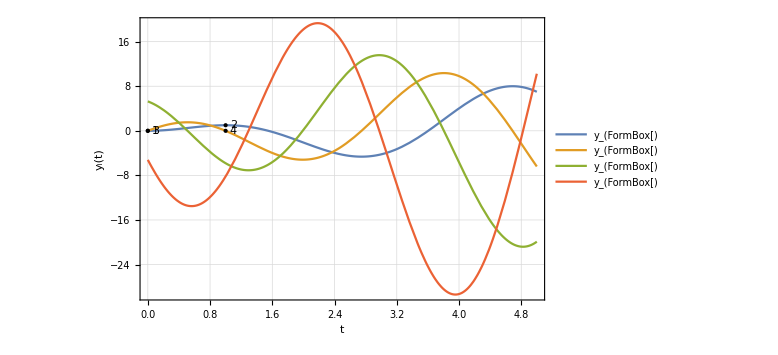

```mathematica
(*Ausgabe*)
plot=Plot[
Evaluate[𝓎[t]/.𝒸𝒫ℓℴ𝓉],{t,𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[1]],𝓉ℬℯ𝓇ℯ𝒾𝒸𝒽[[2]]},
PlotRange->All,Frame->True,FrameLabel->{"t","y_i(t)"},GridLines->Automatic,
PlotLegends->Table[StringForm["y_(``)",i],{i,Length[𝓎[t]]}],
Epilog->
{Table[
Point[{𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]],𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]}],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}],
Table[
Text[i,{𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,2]]+.1,𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃[[i,3]]}],
{i,Length[𝒩ℯ𝒷ℯ𝓃𝒷ℯ𝒹𝒾𝓃ℊ𝓊𝓃ℊℯ𝓃]}]},
ImageSize->Large];
Print[Show[plot]]
```

```mathematica
(*Ausgabe*)
Print[StringForm["y(5) = ``",
𝓎[5][[1]]]]
```

y(5) = 7.00242